# Buildings and Roads Data Extraction

## Generation Routines

## Functions and Libraries

```mathematica
{placeName,filterRatio,clustersNumber}={"Comoros",20,10};
(**)
SetDirectory[NotebookDirectory[]];
shapeFilesPaths={"./SHP/Buildings/","./SHP/Roads/"};
buildingPath=shapeFilesPaths[[1]]<>placeName<>"/"<>placeName<>".shp";
roadPath=shapeFilesPaths[[2]]<>placeName<>"/edges/"<>"edges"<>".shp";
```

## Load Roads Data

```mathematica
rawRoad=Import[roadPath,"Data"][[1,2,2]];
roadsGraphic=Graphics[{Thickness[.003],Purple,Opacity[.75],rawRoad}];
```

## Load Buildings Data

```mathematica
raw=Import[buildingPath,"Data"][[1,2,2]];
dataOriginal=Reverse[Mean/@(#//Transpose)]&/@raw[[All,1,1]];
buildingsPlot=Show[
ListPlot[dataOriginal,
AspectRatio->1,
GridLines->Automatic,
Frame->True,
FrameStyle->Thick,
PlotStyle->{Darker[Blue,.5],PointSize[.01],Opacity[.5]},
ImageSize->1000,
PlotLabel->Style[("Buildings Number: "<>ToString [dataOriginal//Length]),20]
],
roadsGraphic
]
Export["ProbabilitiesMatrices/images/"<>placeName<>"_Buildings_original.png",%,ImageSize->1000]
Export["ProbabilitiesMatrices/"<>placeName<>"_Buildings_Coordinates_original.csv",dataOriginal]
```

-Graphics-

ProbabilitiesMatrices/images/Comoros_Buildings_original.png

ProbabilitiesMatrices/Comoros_Buildings_Coordinates_original.csv

```mathematica
clusters=FindClusters[dataOriginal, Method->"DBSCAN"];
centroids=Mean/@(#//Transpose)&/@clusters;
Show[{
ListPlot[clusters,
GridLines->Automatic,
Frame->True,
AspectRatio->1,
FrameStyle->Thick,
PlotStyle->Directive[{PointSize[.01],Opacity[.5]}],
ImageSize->1000,
PlotLabel->Style[("Buildings Number: "<>ToString [dataOriginal//Length]),20]
],
ListPlot[centroids,PlotStyle->Directive[Black,PointSize[.015],Opacity[.75]]],
roadsGraphic
}]
Export["ProbabilitiesMatrices/images/"<>placeName<>"_Buildings_original_Clustered.png",%,ImageSize->1000]
```

-Graphics-

ProbabilitiesMatrices/images/Comoros_Buildings_original_Clustered.png

```mathematica
clusters=FindClusters[dataOriginal,clustersNumber,Method->"Agglomerate"];
centroids=Mean/@(#//Transpose)&/@clusters;
Show[{
ListPlot[clusters,
GridLines->Automatic,
Frame->True,
AspectRatio->1,
FrameStyle->Thick,
PlotStyle->Directive[{PointSize[.0075],Opacity[.5]}],
ImageSize->1000,
FrameTicksStyle->.01,
PlotLabel->Style[("Buildings Number: "<>ToString [dataOriginal//Length]),0.01]
],
ListPlot[centroids,PlotStyle->Directive[Black,PointSize[.005],Opacity[.05]]],
roadsGraphic
}]
Export["ProbabilitiesMatrices/images/"<>placeName<>"_Buildings_original_Clustered2.png",%,ImageSize->2000,ImageResolution->500]
```

-Graphics-

ProbabilitiesMatrices/images/Comoros_Buildings_original_Clustered2.png

```mathematica
clusteredMap=ListPlot[clusters,PlotStyle->Directive[{PointSize[.002],Opacity[1]}]];
VoronoiMesh[dataOriginal,PlotTheme->"Lines",MeshCellHighlight->{{1,All}->Directive[Blue,Thickness[.0015],Opacity[.2]],{0,All}->None}];
voronoi=Show[%,roadsGraphic,clusteredMap,Graphics[{Black,Opacity[1],PointSize[.0025],Point[dataOriginal]}],ImageSize->1000,AspectRatio->1]
Export["ProbabilitiesMatrices/images/"<>placeName<>"_Buildings_original_Voronoi.png",%,ImageSize->1000]
```

-Graphics-

ProbabilitiesMatrices/images/Comoros_Buildings_original_Voronoi.png

## Filter Number of buildings

```mathematica
range=Range[1,dataOriginal//Length,filterRatio];
data=dataOriginal[[range]];
ListPlot[Table[Callout[data[[i]],i],{i,1,Length[data]}],
AspectRatio->1,
GridLines->Automatic,
Frame->True,
FrameStyle->Thick,
PlotStyle->PointSize[.005],
ImageSize->1000,
PlotLabel->Style[("Buildings Number: "<>ToString [data//Length]),20]
]
Export["ProbabilitiesMatrices/images/"<>placeName<>"_Buildings_filtered.png",%,ImageSize->1000]
Export["ProbabilitiesMatrices/"<>placeName<>"_Buildings_Coordinates_filtered.csv",data]
```

-Graphics-

ProbabilitiesMatrices/images/Comoros_Buildings_filtered.png

ProbabilitiesMatrices/Comoros_Buildings_Coordinates_filtered.csv

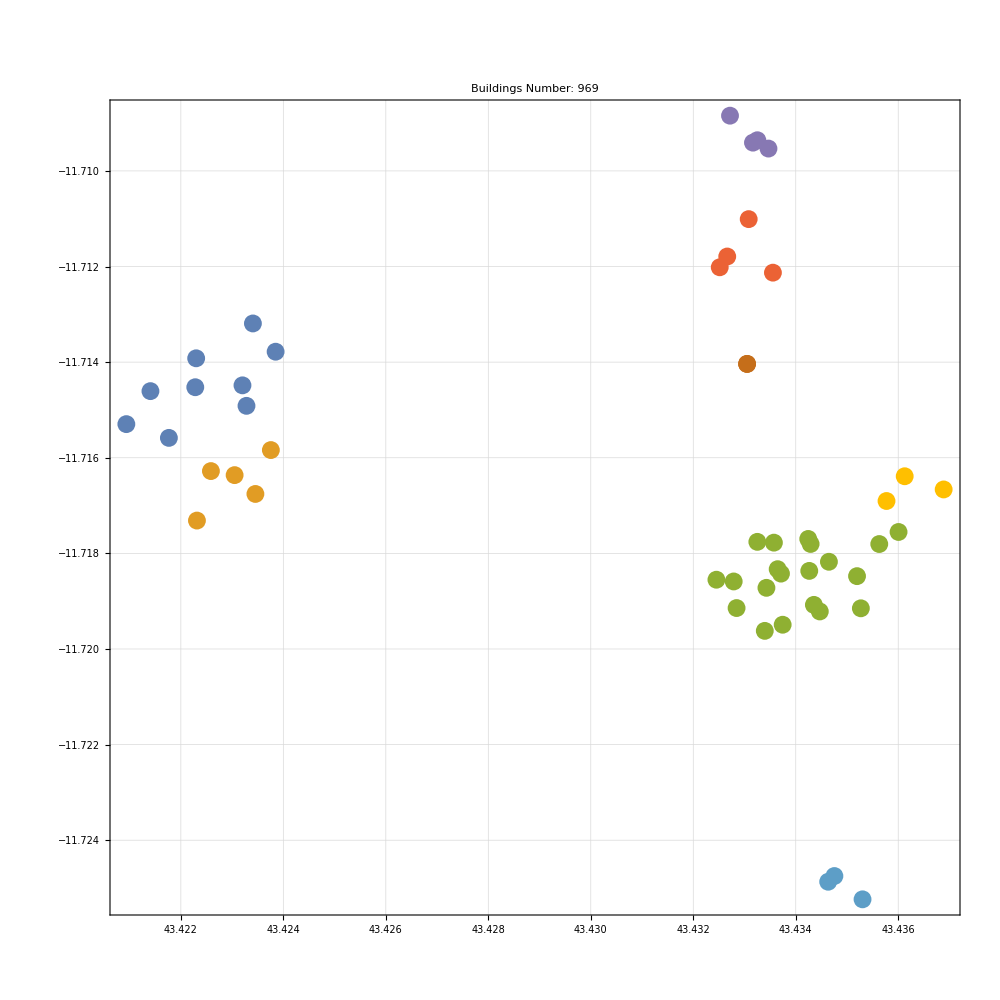

```mathematica
clusters=FindClusters[data, Method->"Spectral"];
ListPlot[clusters,
AspectRatio->1,
GridLines->Automatic,
Frame->True,
FrameStyle->Thick,
ImageSize->1000,
PlotLabel->Style[("Buildings Number: "<>ToString [dataOriginal//Length]),20]
]
```

## Calculate Migration Probabilities

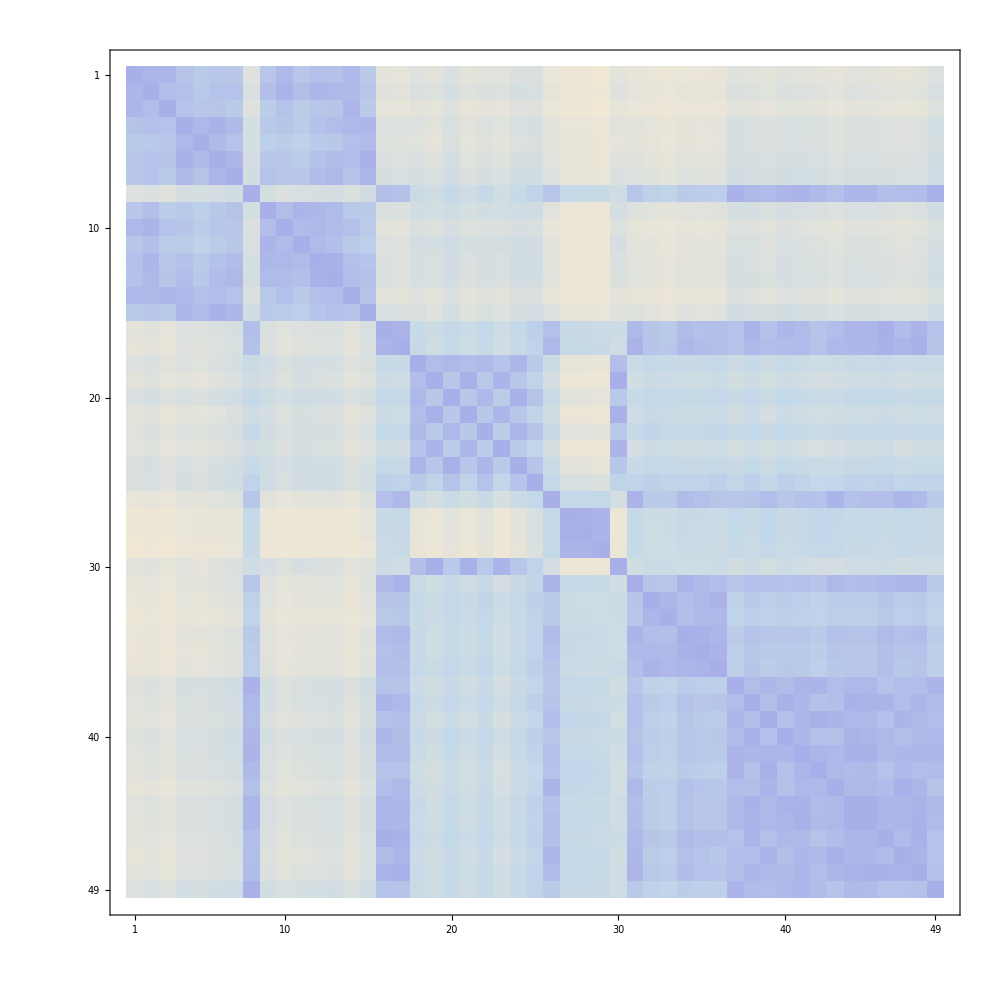

ProbabilitiesMatrices/images/Comoros_Distances_original.png

```mathematica
distances=Table[EuclideanDistance[data[[i]],#]&/@data,{i,1,data//Length}];
distances//MatrixPlot[#,ColorFunction->"LakeColors",BaseStyle->20,ImageSize->1000]&
Export["ProbabilitiesMatrices/images/"<>placeName<>"_Distances_original.png",%,ImageSize->1000]
```

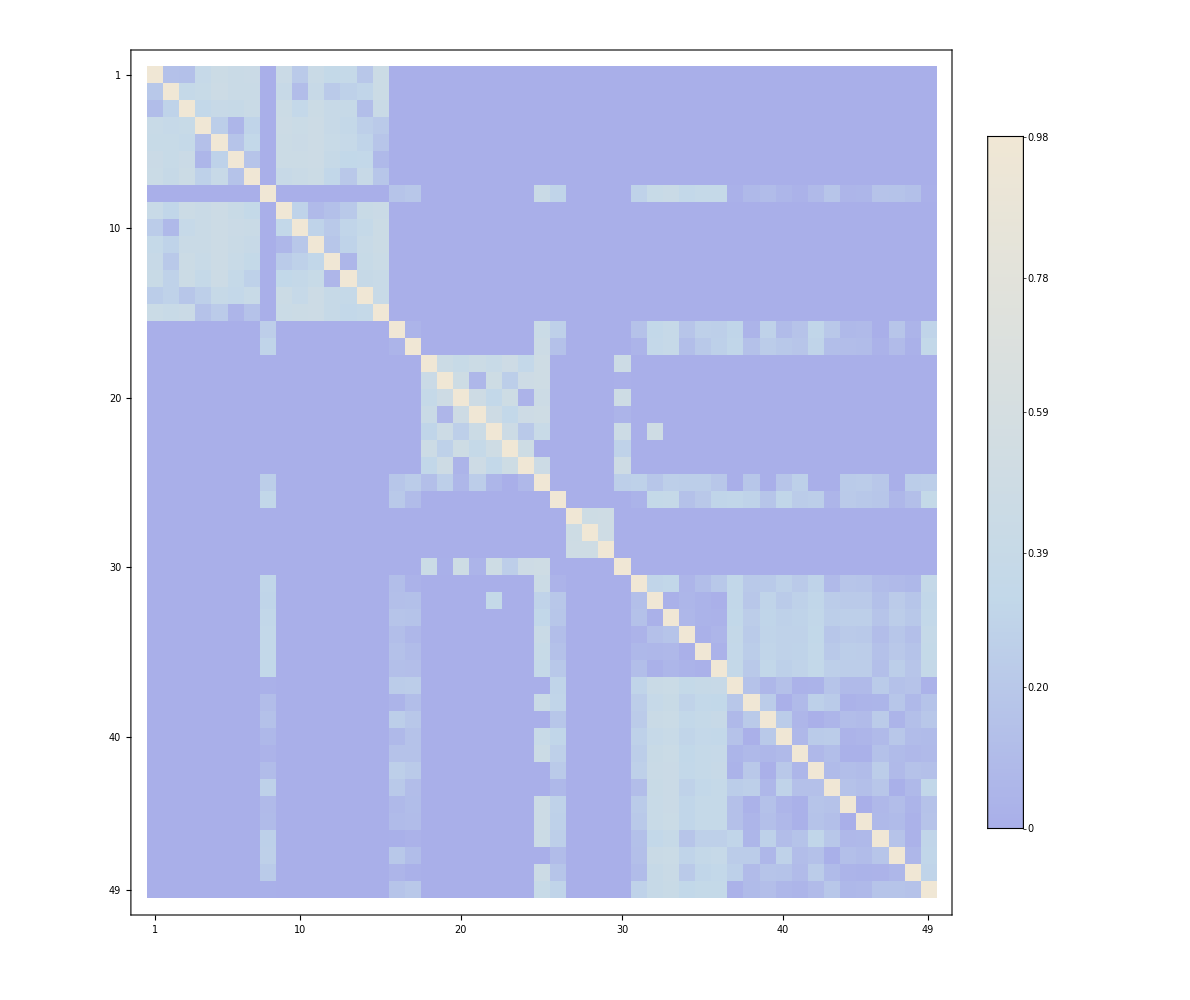

./ProbabilitiesMatrices/Comoros.csv

ProbabilitiesMatrices/images/Comoros_Probabilities_filtered.png

```mathematica
stayForce=50;
thresheld=Table[If[#<.005,#,0]&/@i,{i,distances}];
thresheld//MatrixPlot[#,ColorFunction->"LakeColors",BaseStyle->20,ImageSize->1000]&;
probabilitiesRaw=(#/Total[#])&/@thresheld;
probabilities=((#/Total[#])&/@ReplacePart[probabilitiesRaw,{i_,i_}->stayForce]);
MatrixPlot[probabilities,ColorFunction->"LakeColors",BaseStyle->20,ImageSize->1000,PlotLegends->Automatic]
Export["./ProbabilitiesMatrices/"<>placeName<>".csv",probabilities]
Export["ProbabilitiesMatrices/images/"<>placeName<>"_Probabilities_filtered.png",%%,ImageSize->1000]
```

## Plot Combined Views

```mathematica
roadsAndBuildings=Show[buildingsPlot,roadsGraphic,ImageSize->1000];
combinedView=Show[
buildingsPlot,
roadsGraphic,
Import[buildingPath, "Graphics"],
ImageSize->1000
];
```

```mathematica
grid=Grid[{{Rasterize[combinedView,ImageResolution->2000,ImageSize->1000]},{roadsAndBuildings}}]
Export["ProbabilitiesMatrices/images/"<>placeName<>"CombinedView.png",grid,ImageResolution->250,ImageSize->2000]
```

-Graphics-
-Graphics-

ProbabilitiesMatrices/images/ComorosCombinedView.png